```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools}"}];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
$K = 9;
```

```mathematica
plotsDir = "../../plots/plots-106";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
Do[data[k] = {}, {k, 2, 4}];
Do[Module[{}, (
d = Import["../../runs/Stats-106/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 2, 4}];
)], {$N, 3, 9}]
```

```mathematica
data[2]
```

{{3,0.2400.021},{4,0.2250.006},{5,0.2090.004},{6,0.19820.0019},{7,0.18920.0014},{8,0.18400.0013},{9,0.17820.0013}}

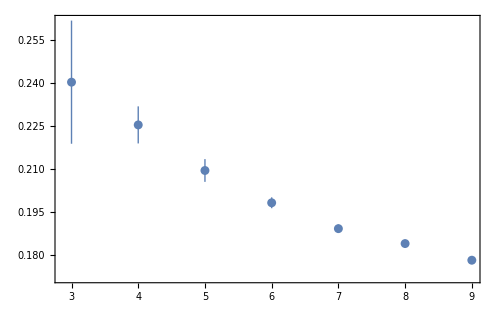

```mathematica
(* Mean of TrX^2 *)
plt1 = ListPlot[data[2],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\sigma_\\text{sim}"},(*
FrameTicks->{{With[{ticks=1.5+0.2Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},*)
ImageSize->500
];
Export[plotsDir<>"/sigma_sim.pdf", plt1, ImageResolution->300];
plt1
```

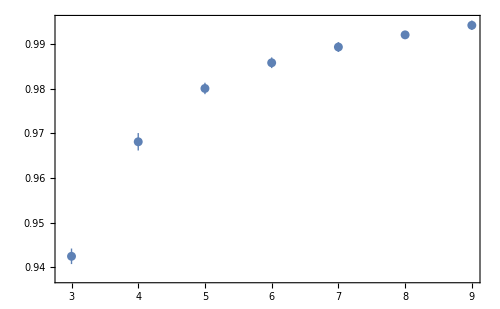

```mathematica
(* SD of TrX^2 *)
plt2 = ListPlot[data[3],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\sigma_\\text{rand}"},(*
FrameTicks->{{With[{ticks=1.5+0.2Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},*)
ImageSize->500
];
Export[plotsDir<>"/sigma_rand.pdf", plt2, ImageResolution->300];
plt2
```

```mathematica
α = {#[[1]], 1/(#[[2]])^2}&/@data[4]
```

{{3,15.42.7},{4,18.41.1},{5,21.90.8},{6,24.70.5},{7,27.30.4},{8,29.10.4},{9,31.10.5}}

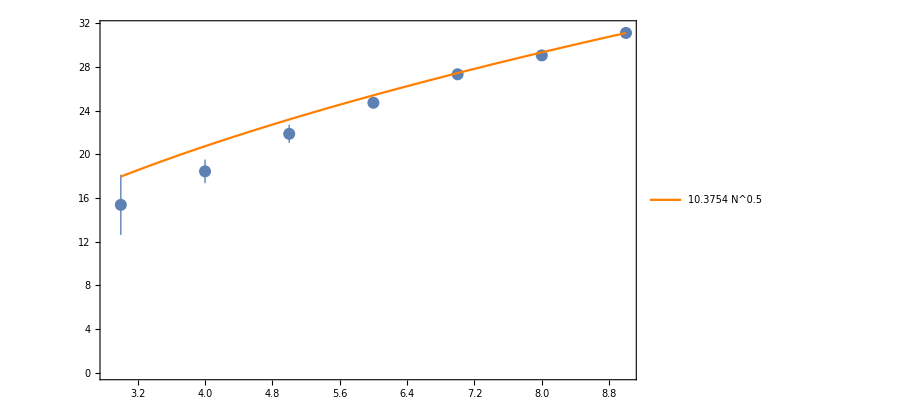

```mathematica
(* SD of TrX^2 *)
plt3 = ListPlot[α,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\alpha"},(*
FrameTicks->{{With[{ticks=1.5+0.2Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},*)
ImageSize->500
];
Export[plotsDir<>"/sigma_rel.pdf", plt3, ImageResolution->300];
Show[plt3, Plot[Exp[lm2[Log[$N]]], {$N, 3, 9}, PlotStyle->Orange, PlotLegends->{Exp[lm2[Log["N"]]]//FullSimplify}]]
```

```mathematica
f
```

{{Log[5],3.08589},{Log[6],3.2081},{Log[7],3.30834},{Log[8],3.36965},{Log[9],3.43805}}

```mathematica
lm2[x_]:=a+0.5x;
```

```mathematica
a = a/.NSolve[a + 0.5Log[9]==3.4380528020107755, a]
```

{2.33944}

```mathematica
f = Log[{#[[1]], #[[2]]["Value"]}&/@α]//Take[#, -5]&
```

{{Log[5],3.08589},{Log[6],3.2081},{Log[7],3.30834},{Log[8],3.36965},{Log[9],3.43805}}

```mathematica
lm = LinearModelFit[f, {$N}, $N]
```

FittedModel[2.1373+0.594727 $N]